# Functional form harvest output vs preciptation

```mathematica
ClearAll[x,a,b,y]
```

## Coefficient functions

x0 = shifts the function across the x axis
L = superior asymptote
k = steepness of the curve

#### Coefficient “a”

```mathematica
ClearAll[L,x0,k,a,b,y, x]
```

```mathematica
L=200
```

200

```mathematica
k=0.005
```

0.005

```mathematica
x0 = 800
```

800

```mathematica
a = La/(1+Exp[-ka(z-x0a)])
```

La/(1+ⅇ^(-ka (-x0a+z)))

```mathematica
a=174.9731/(1+ⅇ^(-0.01710557 (-187.7304+z)))
```

174.973/(1+ⅇ^(-0.0171056 (-187.73+z)))

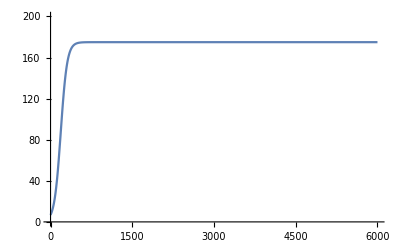

```mathematica
Plot[a,{z,0,6000}, PlotRange->{{0,6000},{0,200}}]
```

#### Coefficient “b”

```mathematica
b = Lb/(1+Exp[-kb(z-x0b)])
```

Lb/(1+ⅇ^(-kb (-x0b+z)))

```mathematica
b=0.5079739/(1+ⅇ^(-0.01097384 (-531.4096+z)))-1.087225
```

-1.08723+0.507974/(1+ⅇ^(-0.0109738 (-531.41+z)))

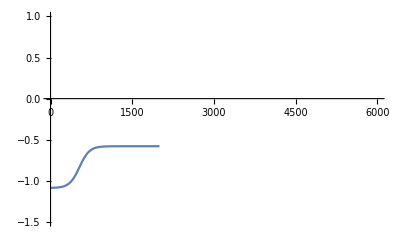

```mathematica
Plot[b,{z,1,2000}, PlotRange->{{0,6000},{-1.5,1}}]
```

#### Where z is precipitation

## Harvest Output function

```mathematica
y = a x Exp[b x]
```

(174.973 ⅇ^((-1.08723+0.507974/(1+ⅇ^(-0.0109738 (-531.41+z)))) x) x)/(1+ⅇ^(-0.0171056 (-187.73+z)))

#### Where x is LSU

## Plotting harvest output vs precipitation

```mathematica
Plot3D[y,{x,0,2.5},{z,0,6000}, AxesLabel->{"LSU","Precipitation"},ColorFunction-> ColorData["DeepSeaColors"]]
```

-Graphics3D-

-Graphics3D-

```mathematica
y/. {x-> 1.8,z-> 5699}
```

111.026